```mathematica
Np=3;
Id=Table[KroneckerDelta[k1,k1p],{k1,0,Np},{k1p,0,Np}];
Sx=Table[KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sy=Table[-I*KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+I*KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sz=Table[KroneckerDelta[k1,k1p]*(2*k1-Np),{k1,0,Np},{k1p,0,Np}];
ghzstate=ArrayReshape[Table[KroneckerDelta[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];
ghzstate=N[Normalize[ghzstate]];
psi0[k1_,k2_,k3_]=(1/Sqrt[2]^(3*Np))*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]];
psi1[k1_,k2_,k3_]=(1/Sqrt[Np+1])*KroneckerDelta[k1,k2]*(1/Sqrt[2]^(Np))*Sqrt[Binomial[Np,k3]];
Urotzx1=MatrixExp[I*Sy*Pi/4.0];
Urotzx=KroneckerProduct[Urotzx1,Urotzx1,Urotzx1];
Urotxz=ConjugateTranspose[Urotzx];
Idbig=KroneckerProduct[Id,Id,Id];
psivec0=ArrayReshape[Table[psi1[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];Hamz=2*(KroneckerProduct[Sz.Sz,Id,Id]+KroneckerProduct[Id,Sz.Sz,Id]+KroneckerProduct[Id,Id,Sz.Sz])-2*(KroneckerProduct[Sz,Sz,Id]+KroneckerProduct[Sz,Id,Sz]+KroneckerProduct[Id,Sz,Sz]);
Hamx1=MatrixPower[(-KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig),2];
Hamx2=(-KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamx3=(KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamx4=(KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamxtest[l_]=(KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+l*Idbig)^2;
```

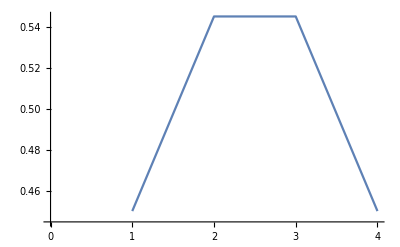

{0.450283,0.545202,0.545202,0.450283}

{0.524734,0.194016,3.52525×10^-17,-2.10162×10^-17,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
hzdiag=Diagonal[Hamz];
hxdiag=Diagonal[Hamx3];
Pzdiag=Table[If[hzdiag[[n]]==0,1,0],{n,1,Length[hzdiag]}];
Pxdiag=Table[If[hxdiag[[n]]==0,1,0],{n,1,Length[hxdiag]}];
Pz=DiagonalMatrix[Pzdiag];
Px=Urotzx.DiagonalMatrix[Pxdiag].Urotxz;
probabilities=Eigenvalues[Pz.Px];
psi=Chop[Eigenvectors[Pz.Px,1][[1]]];
psielem=Table[ArrayReshape[psi,{Np+1,Np+1,Np+1}][[k,k,k]],{k,1,Np+1}];
psielem=Sign[psielem[[1]]]*psielem;
p2=ListPlot[psielem,Joined->True];
Print[p2];
Print[psielem]
Print[probabilities]
```

```mathematica
Px
```

{{0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ},{-0.125+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ},{-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ},{-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ},{-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ},{-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ},{-0.125+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ,-0.125+0. ⅈ},{0.375+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,-0.125+0. ⅈ,0.375+0. ⅈ}}

```mathematica
sol=Eigensystem[Px]
```

{{1.,1.,1.,8.88178×10^-16,7.71415×10^-16,4.12699×10^-16,8.32667×10^-17,0.},{{6.38287×10^-18+0. ⅈ,0.0347794+0. ⅈ,-0.516482+0. ⅈ,0.481702+0. ⅈ,0.481702+0. ⅈ,-0.516482+0. ⅈ,0.0347794+0. ⅈ,0.+0. ⅈ},{-0.319635+0. ⅈ,0.598112+0. ⅈ,-0.113547+0. ⅈ,-0.16493+0. ⅈ,-0.16493+0. ⅈ,-0.113547+0. ⅈ,0.598112+0. ⅈ,-0.319635+0. ⅈ},{0.522335+0. ⅈ,0.126696+0. ⅈ,-0.308794+0. ⅈ,-0.340237+0. ⅈ,-0.340237+0. ⅈ,-0.308794+0. ⅈ,0.126696+0. ⅈ,0.522335+0. ⅈ},{0.328368+0. ⅈ,0.207072+0. ⅈ,-0.403847+0. ⅈ,-0.0376074+0. ⅈ,0.365975+0. ⅈ,0.732215+0. ⅈ,0.121296+0. ⅈ,0.+0. ⅈ},{-0.198536+0. ⅈ,-0.365839+0. ⅈ,0.226163+0. ⅈ,0.039414+0. ⅈ,0.263512+0. ⅈ,0.0767638+0. ⅈ,0.668765+0. ⅈ,0.501462+0. ⅈ},{-0.450676+0. ⅈ,0.50469+0. ⅈ,0.0189603+0. ⅈ,0.172185+0. ⅈ,-0.0116847+0. ⅈ,0.14154+0. ⅈ,-0.34419+0. ⅈ,0.611176+0. ⅈ},{0.370015+0. ⅈ,0.162302+0. ⅈ,0.248353+0. ⅈ,0.75451+0. ⅈ,-0.384495+0. ⅈ,0.121662+0. ⅈ,0.207713+0. ⅈ,0.+0. ⅈ},{0.371131+0. ⅈ,0.408936+0. ⅈ,0.590525+0. ⅈ,-0.151985+0. ⅈ,0.523116+0. ⅈ,-0.219394+0. ⅈ,-0.0378053+0. ⅈ,0.+0. ⅈ}}}

```mathematica
Chop[sol[[2]][[2]]]
```

{-0.319635,0.598112,-0.113547,-0.16493,-0.16493,-0.113547,0.598112,-0.319635}

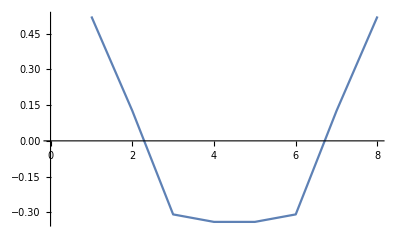

```mathematica
ListPlot[Chop[sol[[2]][[3]]],Joined->True]
```

```mathematica
psicomp=Normalize[Table[N[Binomial[Np,k]^(0.38)],{k,0,Np}]]
```

{0.0568964,0.136485,0.241716,0.350892,0.434038,0.465175,0.434038,0.350892,0.241716,0.136485,0.0568964}

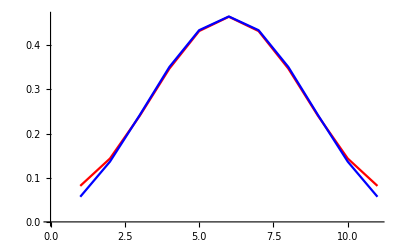

```mathematica
ListPlot[{psielem,psicomp},Joined->True,PlotStyle->{Red,Blue}]
```

#### Trying slightly different Px

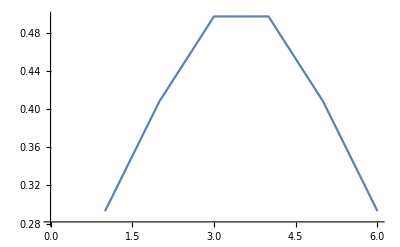

{0.293057,0.408376,0.497339,0.497339,0.408376,0.293057}

```mathematica
hzdiag=Diagonal[Hamz];
hxdiag=Diagonal[Hamxtest[Np]];
Pzdiag=Table[If[hzdiag[[n]]==0,1,0],{n,1,Length[hzdiag]}];
Pxdiag=Table[If[hxdiag[[n]]==0,1,0],{n,1,Length[hxdiag]}];
Pz=DiagonalMatrix[Pzdiag];
Px=Urotzx.DiagonalMatrix[Pxdiag].Urotxz;
psi=Chop[Eigenvectors[Pz.Px,1][[1]]];
psielem=Table[ArrayReshape[psi,{Np+1,Np+1,Np+1}][[k,k,k]],{k,1,Np+1}];
psielem=Sign[psielem[[1]]]*psielem;
p2=ListPlot[psielem,Joined->True];
Print[p2];
Print[psielem]
```